```mathematica
(* Automated extraction of parameters from lineage data *)
```

```mathematica
files=FileNames["*.txt","/home/s1402978/Desktop/volume-dep transcription/Analysis_MC4100_27C/MC4100_27C"];
```

```mathematica
data1=Import[#,"CSV",Delimiters->","]&/@files;
```

```mathematica
Length[data1]
```

54

```mathematica
(* Initialize arrays *)
```

```mathematica
data2=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data2a=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data3a=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data3b=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CycleLength=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Lengthincrement=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
LengthMap=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BirthLength=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BirthLengthCycleData=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DivisionLength=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TAcmeans=Table[0,{i,1,Length[data1]}];
TAcvars=Table[0,{i,1,Length[data1]}];
Weighting = Table[0,{i,1,Length[data1]}];
```

```mathematica
(* Format of data is data1[[lineage number]]{timepoint,divisionindicator,length,per-cell total fluorescence intensity,average fluorescence intensity of the mother cell}. 
Extract the first and second moments of protein fluctuations just before and just after cell division; data2a has the ratios of mean before / mean after; data3 has points {z,2*z1} where z is the FF before division and z1 is the FF after division *)
```

```mathematica
data1[[1]]
```

{{1,1,2.02044,237442,4397.07},{2,0,2.02044,232186,4299.74},{3,0,1.82528,222217,4444.34},{4,0,1.78386,215552,4490.67},3712,{3717,0,3.40784,463668,5095.25},{3718,0,3.42991,464042,5099.36},{3719,0,3.55264,473454,5146.24},{3720,0,3.64352,474723,5104.55}}
 |  |  |  |

```mathematica
For[k=1,k≤Length[data1],k++,
(* take in the data into individual arrays *)
DivisionIndicator=Table[data1[[k]][[i]][[2]],{i,1,Length[data1[[k]]]}];FluorescenseData=Table[data1[[k]][[i]][[4]],{i,1,Length[data1[[k]]]}];LengthData=Table[data1[[k]][[i]][[3]],{i,1,Length[data1[[k]]]}];AppVolData=Table[LengthData[[i]](*Pi*0.5^2*),{i,1,Length[data1[[k]]]}](* assume cyclinder units μm^3 *);Concs= Table[FluorescenseData[[i]]/AppVolData[[i]],{i,1,Length[data1[[k]]]}](* prop to conc *);DivisionTimes=DeleteCases[Table[If[DivisionIndicator[[i]]==1,i,0],{i,1,Length[DivisionIndicator]}],0];
(* begin manipulation of the data *)
CycleLength[[k]]=Table[DivisionTimes[[i+1]]-DivisionTimes[[i]],{i,1,Length[DivisionTimes]-1}];TAcmeans[[k]]=Table[Total[Concs[[DivisionTimes[[i]];;DivisionTimes[[i+1]]]]]/(CycleLength[[k]][[i]]),{i,1,Length[DivisionTimes]-1}] (* time-avg means over each generation *);
TAcvars[[k]]=Table[(Total[Concs[[DivisionTimes[[i]];;DivisionTimes[[i+1]]]]^2]-(TAcmeans[[k]][[i]])^2)/(CycleLength[[k]][[i]]),{i,1,Length[DivisionTimes]-1}](* time-avg variances over each generation *);
(*Weighting=Table[,{i,1,Length[DivisionTimes]-1}];*)
Lengthincrement[[k]]=Table[LengthData[[DivisionTimes[[i+1]]-1]]-LengthData[[DivisionTimes[[i]]]],{i,1,Length[DivisionTimes]-1}];LengthMap[[k]]=Table[{LengthData[[DivisionTimes[[i]]]],LengthData[[DivisionTimes[[i+1]]-1]]},{i,1,Length[DivisionTimes]-1}];BirthLength[[k]]=Table[LengthData[[DivisionTimes[[i]]]],{i,1,Length[DivisionTimes]-1}];DivisionLength[[k]]=Table[LengthData[[DivisionTimes[[i+1]]-1]],{i,1,Length[DivisionTimes]-1}];BirthLengthCycleData[[k]]=Table[Table[LengthData[[i]],{i,DivisionTimes[[j]],DivisionTimes[[j+1]]-1}],{j,1,Length[DivisionTimes]-1}];Fluoafterdiv=Table[FluorescenseData[[DivisionTimes[[i]]]],{i,2,Length[DivisionTimes]}];Fluobeforediv=Table[FluorescenseData[[DivisionTimes[[i]]-1]],{i,2,Length[DivisionTimes]}]; z=N[Variance[Fluobeforediv]/Mean[Fluobeforediv]]; z1=N[Variance[Fluoafterdiv]/Mean[Fluoafterdiv]];y=N[Variance[Fluoafterdiv]-(Variance[Fluobeforediv]/4)];x=N[Mean[Fluobeforediv]];If[y≥0,data2[[k]]={z,2*z1},data2[[k]]=0;];
data2a[[k]]=N[Mean[Fluobeforediv]]/N[Mean[Fluoafterdiv]];];data3=DeleteCases[data2,0];
```

```mathematica
CVmeans = Table[Variance[TAcmeans[[i]]]/Mean[TAcmeans[[i]]],{i,1,Length[TAcmeans]}]; (* coefficient of variation for each lineage of the distribution of time averaged means in each cc generation *)
```

```mathematica
CVvars = Table[Variance[TAcvars[[i]]]/Mean[TAcvars[[i]]],{i,1,Length[TAcvars]}]; (* coefficient of variation for each lineage of the distribution of time averaged variances in each cc generation *)
```

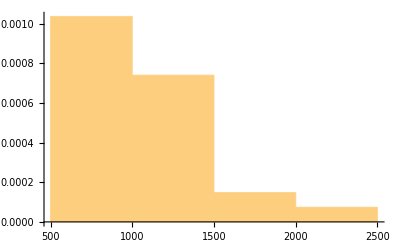

```mathematica
Histogram[CVmeans,Automatic,"PDF"]
```

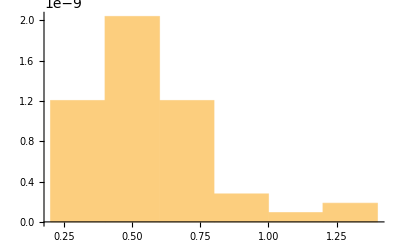

```mathematica
Histogram[CVvars,Automatic,"PDF"]
```

```mathematica
Mean[TAcmeans];
```

```mathematica
mnMns=ListPlot[{Mean[TAcmeans],TAcmeans[[1]],TAcmeans[[2]],TAcmeans[[3]]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed}},Joined->True];
mnVars=ListPlot[{Mean[TAcvars],TAcvars[[1]],TAcvars[[2]],TAcvars[[3]]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed}},Joined->True];
```

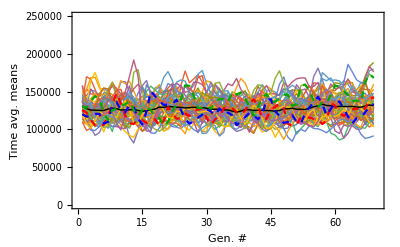

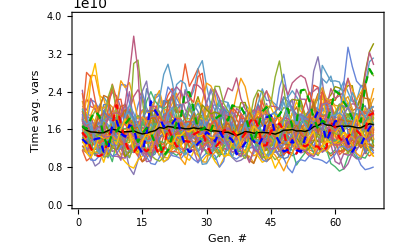

```mathematica
Show[ListPlot[AppendTo[TAcmeans,Mean[TAcmeans]],Joined->True,PlotStyle->Thin,Frame->True,FrameLabel->{"Gen. #","Time avg. means"},PlotRange->{{0,70},{0,250000}}],mnMns]
Show[ListPlot[AppendTo[TAcvars,Mean[TAcvars]],Joined->True,PlotStyle->Thin,Frame->True,FrameLabel->{"Gen. #","Time avg. vars"},PlotRange->{{0,70},{0,4*10^10}}],mnVars]
```

```mathematica
(* Fraction of lineages that are consistent with binomial partitioning with p = 1/2, i.e. they obey the relation 4*Var_after > V_before, i.e. y > 0. This is since binomial partitioning with p = 1/2 implies 4*var_after = var_before + <n>_before  *)
```

```mathematica
N[Length[data3]/Length[data1]]
```

0.574074

```mathematica
(* Using data for those lineages obeying y > 0; Linear plot with slope 1 verifies binomial partitioning with p = 1/2; the intercept is the factor g where fluorescence = g * protein number *)
```

```mathematica
lm=LinearModelFit[data3,x1,x1]
```

FittedModel[2117.97+1.18677 x1]

```mathematica
lm["RSquared"]
```

0.901901

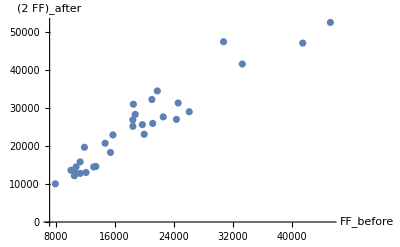

```mathematica
ListPlot[data3,PlotRange->All,AxesLabel->{Subscript[FF,before],Subscript[2*FF,after]}]
```

```mathematica
(* Ratio of protein before and after cell division for ALL lineages; a value of 2 is indication of binomial partitioning with probability of 1/2; note that the mean is greater than 2 on average showing the mother cell has more molecules after partitioning than daughter cells *)
```

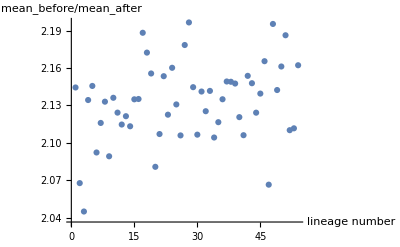

```mathematica
ListPlot[data2a,AxesLabel->{"lineage number",Subscript[mean,before]/Subscript[mean,after]}]
```

```mathematica
(* Fitting Erlang distribution of cell cycle length times; data from all lineages is pooled together *)
```

```mathematica
paramserlang=FindDistributionParameters[Flatten[CycleLength],GammaDistribution[α,β]]
```

{α→29.4575,β→1.81433}

```mathematica
N[Mean[Flatten[CycleLength]]]
```

53.4455

```mathematica
N[Variance[Flatten[CycleLength]]/Mean[Flatten[CycleLength]]^2]
```

0.0355389

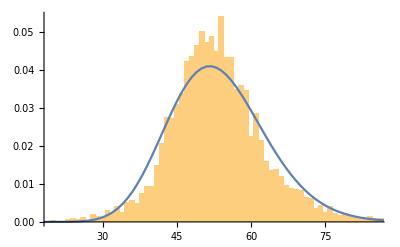

```mathematica
Show[Histogram[Flatten[CycleLength],{1},"PDF"],ListPlot[Table[{x,PDF[GammaDistribution[α,β]/.paramserlang,x]},{x,1,140}],Joined->True]]
```

```mathematica
Variance[GammaDistribution[α,β]/.{α->29.457455104443518,β->1.8143290991110723}]
```

96.9678

```mathematica
Mean[GammaDistribution[α,β]/.{α->29.457455104443518,β->1.8143290991110723}]
```

53.4455

```mathematica
(* Autocorrelation of cell cycles lengths; there are more negative correlated successive cell cycle lengths than expected by chance; correlation is 7 standard deviations away from mean and hence there is probability of 1 in 390682215445 that it can be explained by chance! however the correlation is weak *)
```

```mathematica
N[CorrelationFunction[Flatten[CycleLength],1]]
```

-0.111018

```mathematica
data4=Table[0,{i,5000}];
```

```mathematica
For[k=1,k≤5000,k++,rnddata=Table[RandomVariate[ErlangDistribution[α,β]/.paramserlang,Length[CycleLength[[i]]]],{i,Length[CycleLength]}];data4[[k]]=N[CorrelationFunction[Flatten[rnddata],1]];]
```

ErlangDistribution::pintprm: Parameter 29.4575 at position 1 in ErlangDistribution[29.4575,1.81433] is expected to be a positive integer.

General::stop: Further output of ErlangDistribution::pintprm will be suppressed during this calculation.

```mathematica
Histogram[data4]
```

-Graphics-

```mathematica
7*StandardDeviation[data4]
```

Indeterminate

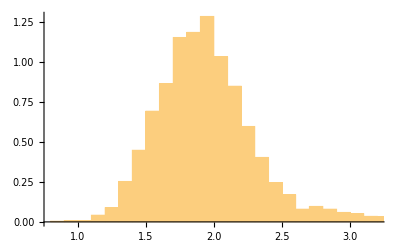

```mathematica
(* Find distribution of length increment from birth to division; does not support an adder where a constant volume is added in each cell cycle *)

Show[Histogram[Flatten[Lengthincrement],Automatic,"PDF"]]
```

```mathematica
StandardDeviation[Flatten[Lengthincrement]]/Mean[Flatten[Lengthincrement]]
```

0.260573

```mathematica
(* Find relationship between final and initial lengths *)
```

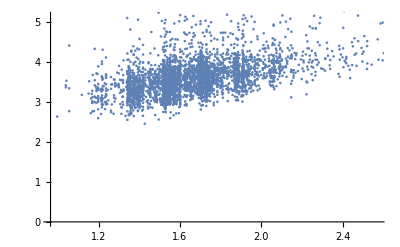

```mathematica
ListPlot[Flatten[LengthMap,1]]
```

```mathematica
lm1=LinearModelFit[Flatten[LengthMap,1],x1,x1]
```

FittedModel[1.95537+1.02236 x1]

```mathematica
lm1["RSquared"]
```

0.298634

```mathematica
(* Calculating the birth length distribution *)
```

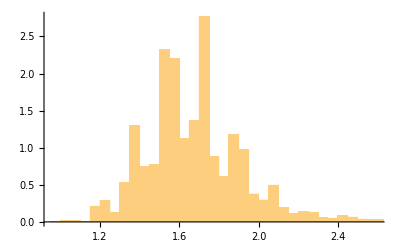

```mathematica
plbl=Histogram[Flatten[BirthLength],Automatic,"PDF"]
```

```mathematica
Mean[Flatten[BirthLength]]
```

1.70452

```mathematica
Variance[Flatten[BirthLength]]/Mean[Flatten[BirthLength]]
```

0.0644732

```mathematica
parambl=FindDistributionParameters[Flatten[BirthLength],GammaDistribution[a,b]]
```

{a→31.9815,b→0.053297}

```mathematica
paramln=FindDistributionParameters[Flatten[BirthLength],LogNormalDistribution[a,b]]
```

{a→0.517567,b→0.170912}

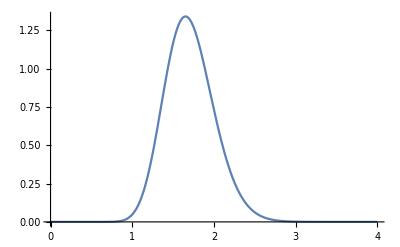

```mathematica
plgammabl=Plot[PDF[GammaDistribution[a,b]/.parambl,h],{h,0,4}]
```

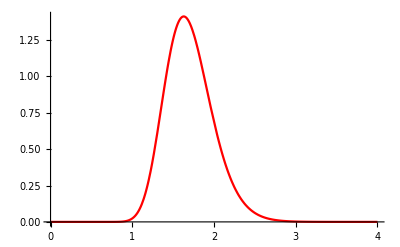

```mathematica
pllnbl=Plot[PDF[LogNormalDistribution[a,b]/.paramln,h],{h,0,4},PlotStyle->Red]
```

```mathematica
bestfitbl=PDF[FindDistribution[Flatten[BirthLength]],h]
```

0.0504859 ⅇ^(-0.966031 (-2.35553+h)^2)+1.60972 ⅇ^(-9.85287 (-1.65814+h)^2)

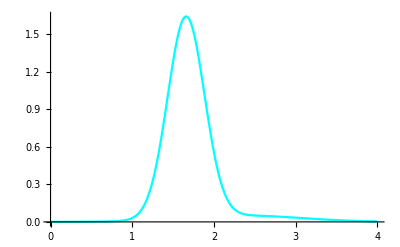

```mathematica
plmixed=Plot[bestfitbl,{h,0,4},PlotStyle->Cyan]
```

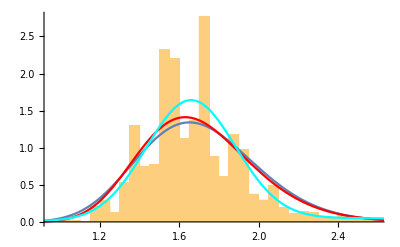

```mathematica
Show[plbl,plgammabl,pllnbl,plmixed]
```

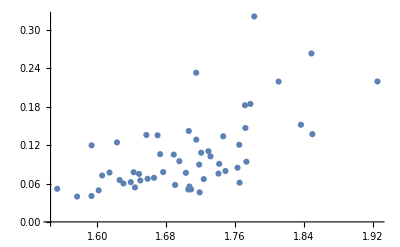

```mathematica
ListPlot[Table[{Mean[BirthLength[[i]]],Variance[BirthLength[[i]]]},{i,1,Length[BirthLength]}]]
```

```mathematica
LinearModelFit[Table[{Mean[BirthLength[[i]]],Variance[BirthLength[[i]]]},{i,1,Length[BirthLength]}],h,h]
```

FittedModel[-0.728708+0.489583 h]

```mathematica
(* The length grows exponential with cellular time; fit length vs cellular time to exponential fn and report Rsquared of plot. Mean Rsquared (calculated across cell cycles and lineages) is very close 1.  *)
```

```mathematica
datA1=Table[Table[Table[{i,BirthLengthCycleData[[w]][[j]][[i]]},{i,1,Length[BirthLengthCycleData[[w]][[j]]]}],{j,1,Length[BirthLengthCycleData[[w]]]}],{w,1,Length[BirthLengthCycleData]}];
```

```mathematica
datA2=Table[Table[NonlinearModelFit[datA1[[w]][[i]],a*Exp[-b*h],{a,b},h]["RSquared"],{i,1,Length[datA1]}],{w,1,Length[BirthLengthCycleData]}];
```

```mathematica
Mean[Flatten[datA2]]
```

0.99857

```mathematica
Variance[Flatten[datA2]]
```

3.67412×10^-7

```mathematica
(* The growth rate is extracted by fitting exponential fn to length vs time curves for each cell cycle in each lineage *)
```

```mathematica
datA3=Table[Table[Coefficient[FullSimplify[Log[Normal[NonlinearModelFit[datA1[[w]][[i]],a*Exp[-b*h],{a,b},h]]],Assumptions->h>0],h],{i,1,Dimensions[datA1][[2]]}],{w,1,Dimensions[datA1][[1]]}];
```

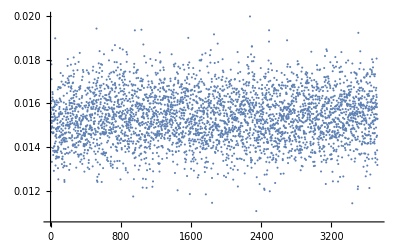

```mathematica
ListPlot[Flatten[datA3]]
```

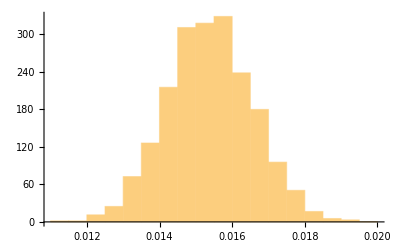

```mathematica
Histogram[Flatten[datA3],Automatic,"PDF"]
```

```mathematica
Dimensions[datA3]
```

{54,69}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1402978/Desktop/Tanouchi-Inference-Project/Julia_analysis

```mathematica
datA3;
```

```mathematica
Export["exp_grs_all_27.csv",datA3,"CSV"]
```

exp_grs_all_27.csv

```mathematica
(* Calculating ratio of birth length at generation i to division length at generation i - 1 *)
```

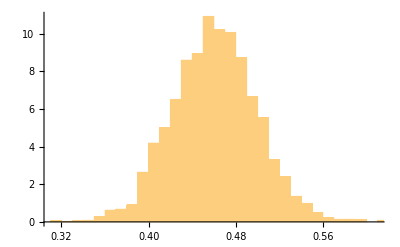

```mathematica
plratio1=Histogram[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]],Automatic,"PDF"]
```

```mathematica
Mean[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]]]
```

0.460796

```mathematica
StandardDeviation[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]]]
```

0.0390425

```mathematica
paramsratio=FindDistributionParameters[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]],BetaDistribution[μ,σ]]
```

{μ→74.5543,σ→87.235}

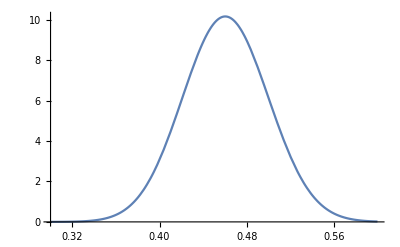

```mathematica
plratio2=Plot[PDF[BetaDistribution[μ,σ]/.paramsratio,h],{h,0.30,0.60}]
```

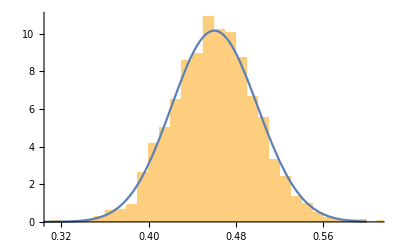

```mathematica
Show[{plratio1,plratio2}]
```

```mathematica
(* Calculating theta *)
```

```mathematica
DivisionLength[[20]]
```

{3.48349,3.28801,3.30246,3.58704,3.72697,3.49698,4.32894,4.90938,4.83705,4.16358,3.37079,3.31717,3.04477,3.60962,3.77072,4.11269,3.86665,3.7457,3.50241,3.19068,3.5417,3.39705,3.82592,3.86574,6.70337,4.95852,4.11675,4.48774,4.28645,5.68431,4.48113,4.41861,3.88782,4.2551,3.88988,3.73059,3.51659,3.31346,3.39385,3.56322,3.63415,3.48493,4.6416,6.32869,6.91082,3.93625,4.17285,3.7575,4.73553,4.01944,4.02874,3.89378,3.7072,3.96968,7.00779,5.72029,4.97433,3.99126,3.65738,3.6165,3.67994,3.49831,3.94942,3.75174,3.78498,3.90176,3.68199,3.83075,3.73698}

```mathematica
BirthLength[[20]]
```

{1.34508,1.7071,1.53008,1.47113,1.69751,1.52537,1.62618,2.06038,2.26759,2.23766,1.8704,1.66653,1.47362,1.57547,1.93404,1.60698,1.90738,1.95622,1.93848,1.52479,1.43008,1.65292,1.57547,1.66569,1.96702,3.58879,2.15038,2.09064,1.99251,2.0423,2.85534,2.08618,2.24712,1.70206,1.85052,1.85114,1.70098,1.81063,1.51601,1.49674,1.56958,1.65173,1.50673,3.20932,3.43391,2.54232,1.90982,2.09133,1.8121,2.0496,1.79392,1.93668,1.75913,1.64564,1.98236,3.14191,2.90298,2.4159,2.01276,1.55402,1.61728,1.90738,1.8766,1.82821,1.53008,1.55097,1.7693,1.93901,1.7323}

```mathematica
CycleLength[[20]]
```

{58,45,55,57,56,58,67,51,47,41,43,49,52,59,53,55,43,44,45,56,55,49,65,62,84,24,40,57,52,67,28,51,36,61,47,48,44,46,59,55,50,49,79,46,47,29,62,44,65,49,49,52,54,60,79,44,34,34,44,59,52,47,47,48,48,59,52,50,43}

```mathematica
Lambda=(DivisionLength[[20]]/BirthLength[[20]])
```

{2.5898,1.92608,2.15836,2.43829,2.19555,2.29255,2.66203,2.38275,2.13312,1.86068,1.80218,1.99047,2.06618,2.29114,1.94966,2.55927,2.0272,1.91476,1.80678,2.09254,2.47657,2.05518,2.42843,2.3208,3.40788,1.38167,1.91443,2.14659,2.15128,2.78329,1.56939,2.11804,1.73013,2.49997,2.10205,2.01529,2.06739,1.83,2.23867,2.38065,2.31536,2.10987,3.08058,1.97197,2.01252,1.54829,2.18494,1.7967,2.61328,1.96109,2.24577,2.01054,2.10741,2.41224,3.53507,1.82064,1.71353,1.65208,1.8171,2.32719,2.27539,1.83409,2.10456,2.05214,2.47371,2.51569,2.08104,1.97562,2.15724}

```mathematica
Mean[Lambda/BirthLength[[20]]]
```

1.19485

```mathematica
Theta=1/(BirthLength[[20]]*(1 + BirthLength[[20]]/Lambda)*Log[1+Lambda/BirthLength[[20]]])
```

{0.455842,0.411152,0.434652,0.433779,0.400262,0.429068,0.393695,0.3387,0.322391,0.335278,0.388826,0.415576,0.451988,0.418909,0.37231,0.401257,0.373059,0.37049,0.377876,0.43916,0.441104,0.415,0.412746,0.400499,0.320659,0.237818,0.343981,0.343015,0.355844,0.328445,0.283592,0.344613,0.339061,0.386779,0.378692,0.382294,0.405474,0.397456,0.433656,0.430954,0.418966,0.412604,0.400319,0.247582,0.233288,0.313023,0.366324,0.356336,0.364977,0.35537,0.381754,0.36937,0.393419,0.400243,0.315746,0.255461,0.275619,0.322607,0.366417,0.421545,0.411487,0.381455,0.374539,0.384373,0.419782,0.413776,0.392858,0.370475,0.395835}

```mathematica
Mean[Theta]
```

0.374804

```mathematica
Covariance[Theta,CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.00400915

```mathematica
Mean[Theta]+Covariance[Theta,CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.378814

```mathematica
Mean[Theta*CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.378755

```mathematica
0.72/Mean[BirthLength[[20]]]
```

0.373907

```mathematica
1/Mean[Flatten[BirthLengthCycleData[[20]]]]
```

0.364577